```mathematica
Clear["Global`*"]
<<Notation`
(*Physical constants in cgs units*)
G=6.67 10^-8;  (*Newton's constant in cgs*)
c=3 10^10 ; (*Speed of light in cgs*)
κr=1.6 10^24;
kb=1.38 10^-16;
mp=1.67 10^-24;
(*Stefan-Boltzmann constant in cgs*)
σ=5.67 10^-5;
h=6.63 10^-27;
Msun=2 10^33;
(*Special symbols*)
Symbolize[Subscript[M, 7]]
Symbolize[Subscript[ϵ, 0.1]]
Symbolize[κ̂]
Symbolize[Subscript[α, 0.3]]
```

```mathematica
γ=4./3.;
κr=1.6 10^24;
Subscript[M, 7]=1;
M=10^7 Msun Subscript[M, 7];
Rs=2 G M/c^2;
r3=Range[0.1, 2, 0.1]
R=r3 1000 Rs;
Ω=√(G M/R^3);
μ0=0.615;
μe=1;
κ̂=1;
κes=0.4 μe;
√(140 c κr/(γ σ κes))
Subscript[f, T]=3/8;
Subscript[α, 0.3]=1;
Subscript[ϵ, 0.1]=1;
Subscript[L, Edd]=4π G Subscript[M, 7]/(κes κ̂)c 10^7 Msun;

Subscript[Ṁ, Edd]=Subscript[L, Edd]/(c^2 Subscript[ϵ, 0.1] 0.1);
ṁ=0.1;   
Ṁ=ṁ*Subscript[Ṁ, Edd];
Print["Ṁ= ",Ṁ]
(*Constant out front is probably slightly difference if the μe dependence is not include*)
Σ=(169123  μ0^(4/5) ((ṁ)/Subscript[ϵ, 0.1])^(3/5))/(μe^(4/5) (κ̂)^(6/5) ((r3^3 Subscript[f, T])/Subscript[M, 7])^(1/5)( Subscript[α, 0.3])^(4/5));
Print["Σ= ", Σ]

ν=(Ṁ)/(3π Σ);
Print["ν= ", ν]
Export["Parameters", Table[{Round[ Σ[[i]],1], 0.1, Round[1000 r3[[i]], 1]}, {i, 1, Σ//Length} ], "Table"]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

4.71405×10^20

Ṁ= 1.39696×10^24

Σ= {139475.,92019.2,72147.9,60710.,53102.4,47599.9,43394.8,40053.7,37320.8,35034.5,33087.3,31404.2,29931.6,28629.9,27468.9,26425.6,25481.6,24622.5,23836.6,23114.2}

ν= {1.06271×10^18,1.61077×10^18,2.05442×10^18,2.44148×10^18,2.79125×10^18,3.11392×10^18,3.41567×10^18,3.70059×10^18,3.97157×10^18,4.23074×10^18,4.47974×10^18,4.71982×10^18,4.95202×10^18,5.17718×10^18,5.396×10^18,5.60904×10^18,5.81683×10^18,6.01978×10^18,6.21826×10^18,6.41261×10^18}

Parameters

```mathematica
κs=Table[4.7 10^20 Ω[[i]] Tp1^(-15/4), {i, 1, Σ//Length}];
(*κs=1.83 10^9 Ω (Tp)^(-9/4)*)
ϵs=κs/(κs+κes);
Ξ=(0.873 ϵs^(-1/6))/(1-0.127 ϵs^(5/6))1/(1+(ϵs^-1-1)^(2/3));

r1=Table[FindRoot[9/8 ν [[i]]Σ[[i]] Ω[[i]]^2 ==Ξ[[i]] σ Tp1^4,{Tp1,(9/8 ν[[i]] Σ[[i]] Ω[[i]]^2/σ )^0.25}], {i, 1, Length[Σ]}];
Tp=Tp1/.r1
κs=Table[4.7 10^20 Ω[[i]] Tp[[i]]^(-15/4), {i, 1, Σ//Length}];
(*κs=1.83 10^9 Ω (Tp)^(-9/4)*)
ϵs=κs/(κs+κes);

x=(1+1/ϵs)^-1;
ξ=h ν1/(kb Tp);
f=ξ^-3(1-ⅇ^-ξ);
Kν=-1/3+2^(1/3)/(3 (-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))+((-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))/(3 2^(1/3));
ϵν=(1+1/Kν)^-1;
(*Peak freqency. Note this is approximate, as it it is technically only applicable in for a blackbody. *)
νmax=2.82 kb Tp/h;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

{26071.,13883.7,9771.02,7670.37,6380.59,5500.91,4858.7,4367.03,3977.15,3659.54,3395.2,3171.36,2979.06,2811.87,2664.98,2534.79,2418.49,2313.9,2219.27,2133.18}

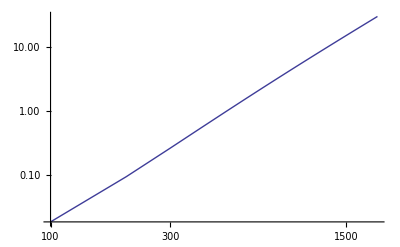

```mathematica
ρp=Table[(3 c Ω[[i]]^2)/(4 γ σ Tp[[i]]^4  Kν[[i]] κes^2(1+Kν[[i]]))/.ν1->νmax[[i]], {i, 1, Σ//Length}];
p1=Transpose[{R/Rs, (ρp kb  Tp/(μ0 mp))/( 4 σ Tp^4/(3c))}]//ListLogLogPlot[#, PlotRange->{{100, 2000}, Automatic}, Joined->True]&
(*p2=Transpose[{R/Rs, 4 σ Tp^4/(3c)}]//ListLinePlot[#, PlotStyle->Directive[Red]]&;
Show[p1,p2]*)
```

{139475.,92019.2,72147.9,60710.,53102.4,47599.9,43394.8,40053.7,37320.8,35034.5,33087.3,31404.2,29931.6,28629.9,27468.9,26425.6,25481.6,24622.5,23836.6,23114.2}

{7.15588×10^-6,2.52999×10^-6,1.37715×10^-6,8.94485×10^-7,6.40041×10^-7,4.86896×10^-7,3.86381×10^-7,3.16248×10^-7,2.65033×10^-7,2.26289×10^-7,1.96143×10^-7,1.72144×10^-7,1.52668×10^-7,1.36606×10^-7,1.23176×10^-7,1.11811×10^-7,1.02091×10^-7,9.37031×10^-8,8.64037×10^-8,8.00052×10^-8}

{1.06271×10^18,1.61077×10^18,2.05442×10^18,2.44148×10^18,2.79125×10^18,3.11392×10^18,3.41567×10^18,3.70059×10^18,3.97157×10^18,4.23074×10^18,4.47974×10^18,4.71982×10^18,4.95202×10^18,5.17718×10^18,5.396×10^18,5.60904×10^18,5.81683×10^18,6.01978×10^18,6.21826×10^18,6.41261×10^18}

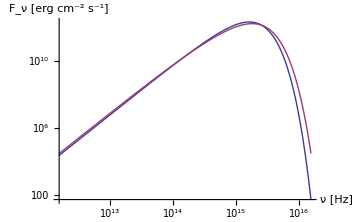
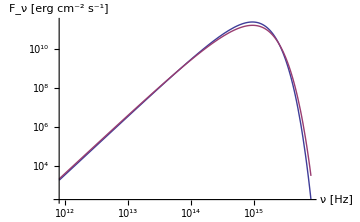
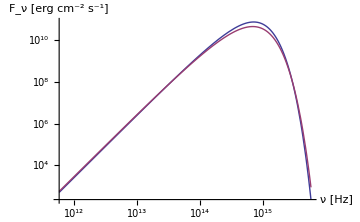
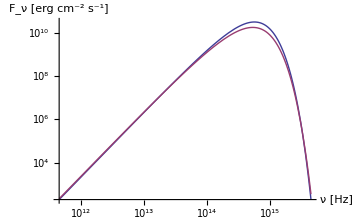

```mathematica
Σtmp=Σ
Σ=Σ[[1;;4]];
Ωtmp=Ω
Ω=Ω[[1;;4]];
νtmp=ν
ν=ν[[1;;4]];
Tp=Tp[[1;;4]];
Kν=Kν[[1;;4]];
ϵν=ϵν[[1;;4]];
Tpblack=(9/8 ν Σ Ω^2/σ)^(1/4);

(*Peak freqency. Note this is approximate, as it it is technically only applicable in for a blackbody. *)
νmax=2.82 kb Tp/h;
B1=(2 h ν1^3/c^2)/(E^((h ν1)/( kb Tpblack))-1);
B2=(2 h ν1^3/c^2)/(E^((h ν1)/( kb Tp))-1);
Table[LogLogPlot[{B1[[i]] ν1, 2 ϵν[[i]]^(1/2)/(1+ϵν[[i]]^(1/2))B2[[i]] ν1//Re},  {ν1, 0.001 νmax[[i]], 10νmax[[i]]}, ImageSize->Medium, AxesLabel->{"ν [Hz]", "F_ν  [erg cm^-2 s^-1]"}], {i,1, Σ//Length}]
ν=νtmp;
Ω=Ωtmp;
Σ=Σtmp;
```

{139475.,92019.2,72147.9,60710.,53102.4,47599.9,43394.8,40053.7,37320.8,35034.5,33087.3,31404.2,29931.6,28629.9,27468.9,26425.6,25481.6,24622.5,23836.6,23114.2}

{7.15588×10^-6,2.52999×10^-6,1.37715×10^-6,8.94485×10^-7,6.40041×10^-7,4.86896×10^-7,3.86381×10^-7,3.16248×10^-7,2.65033×10^-7,2.26289×10^-7,1.96143×10^-7,1.72144×10^-7,1.52668×10^-7,1.36606×10^-7,1.23176×10^-7,1.11811×10^-7,1.02091×10^-7,9.37031×10^-8,8.64037×10^-8,8.00052×10^-8}

{1.06271×10^18,1.61077×10^18,2.05442×10^18,2.44148×10^18,2.79125×10^18,3.11392×10^18,3.41567×10^18,3.70059×10^18,3.97157×10^18,4.23074×10^18,4.47974×10^18,4.71982×10^18,4.95202×10^18,5.17718×10^18,5.396×10^18,5.60904×10^18,5.81683×10^18,6.01978×10^18,6.21826×10^18,6.41261×10^18}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

{39920.4,35383.6,31872.6,29066.,26765.5,24841.7,23206.4,21797.3,20569.,19487.9,18528.,17669.5,16896.5,16196.5,15559.2}

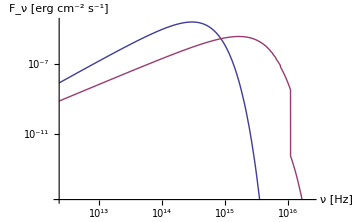
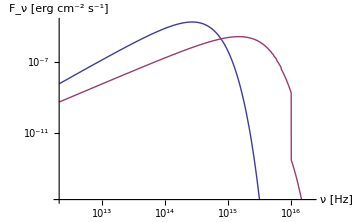
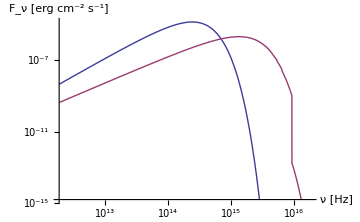
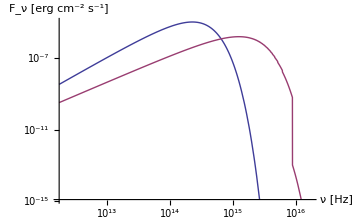
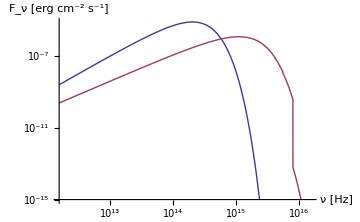
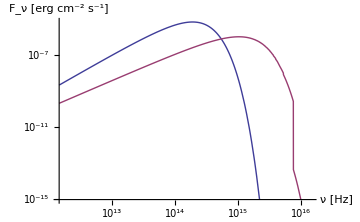
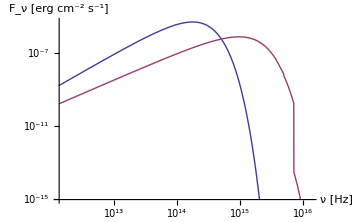
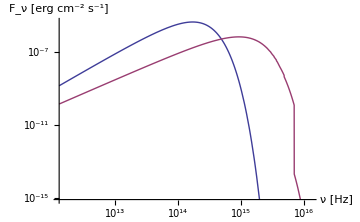
Null.{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Σtmp=Σ
Σ=Σ[[6;;]];
Ωtmp=Ω
Ω=Ω[[6;;]];
νtmp=ν
ν=ν[[6;;]];
Tpblack=(9/8 ν Σ Ω^2/σ)^(1/4);
κs=1.83 10^9 Ω (Tp1)^(-9/4);
ϵs=κs/(κs+κes);
Ξ=(0.873 ϵs^(-1/6))/(1-0.127 ϵs^(5/6))1/(1+(ϵs^-1-1)^(2/3));

r1=Table[FindRoot[9/8 ν [[i]]Σ[[i]] Ω[[i]]^2 ==Ξ[[i]] σ Tp1^4,{Tp1,(9/8 ν[[i]] Σ[[i]] Ω[[i]]^2/σ )^0.25}], {i, 1, Length[Σ]}];
Tp=Tp1/.r1
κs=Table[1.83 10^9 Ω[[i]] Tp[[i]]^(-9/4), {i, 1, Σ//Length}];
(*κs=1.83 10^9 Ω (Tp)^(-9/4)*)
ϵs=κs/(κs+κes);

x=(1+1/ϵs)^-1;
ξ=h ν1/(kb Tp);
f=ξ^-3(1-ⅇ^-ξ);
Kν=-1/3+2^(1/3)/(3 (-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))+((-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))/(3 2^(1/3));
ϵν=(1+1/Kν)^-1;

(*Peak freqency*)
νmax=2.82 kb Tp/h;

(*Peak freqency. Note this is approximate, as it it is technically only applicable in for a blackbody. *)
νmax=2.82 kb Tp/h;
B1=(2 h ν1^3/c^2)/(E^((h ν1)/( kb Tpblack))-1);
B2=(2 h ν1^3/c^2)/(E^((h ν1)/( kb Tp))-1);.
Table[LogLogPlot[{B1[[i]] , 2 ϵν[[i]]^(1/2)/(1+ϵν[[i]]^(1/2))B2[[i]] //Re},  {ν1, 0.001 νmax[[i]], 10νmax[[i]]}, ImageSize->Medium, AxesLabel->{"ν [Hz]", "F_ν  [erg cm^-2 s^-1]"}], {i,1, Σ//Length}]
ν=νtmp;
Ω=Ωtmp;
Σ=Σtmp;
```

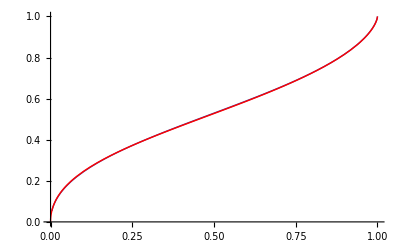

```mathematica
Module[{ξ, Ξ, ϵs, Kν, f, ϵ, p1, p2}, 
Kν=(y/.(Solve[y^2(1+y)==(1-1/ϵs)^-2 f, y][[1]]));
ϵ=(1+Kν^-1)^-1;
f=ξ^-3(1-ⅇ^-ξ);
p1=Plot[15/π^4 NIntegrate[2 ϵ^(1/2)/(1+ϵ^(1/2)) ⅇ^-ξ/f, {ξ, 0, ∞}], {ϵs, 0, 1}, AxesOrigin->{0, 0}];
p2=Plot[(0.873 ϵs^(-1/6))/(1-0.127 ϵs^(5/6))1/(1+(ϵs^-1-1)^(2/3)), {ϵs, 0, 1}, PlotStyle->Directive[Red]];
Show[p1, p2]
]

(*Ξ=15/π^4(∫_0)^∞2 ϵ^(1/2)/(1+ϵ^(1/2))ⅇ^-ξ dξ/f*)
(*2 ϵ^(1/2)/(1+ϵ^(1/2)) ⅇ^-ξ/f//Simplify//TraditionalForm*)
```